```mathematica
list7 = ParallelTable[{vv,findProbVexact[.6,4,-vv,0]},{vv,-6,3,.1}];
list8 =ParallelTable[ {vv,Exp[findProbVapproxWork2[.6,4,-vv,0]]},{vv,-6,3,.1}];
```

```mathematica
list8 =ParallelTable[ {vv,Exp[findProbVapproxWork2[.6,4,-vv,0,0.00001]]},{vv,-6,3,.1}]
```

{{-6.,9.84597×10^-12},{-5.9,1.66467×10^-11},{-5.8,2.78294×10^-11},{-5.7,4.60086×10^-11},{-5.6,7.52071×10^-11},{-5.5,1.21563×10^-10},{-5.4,1.94279×10^-10},{-5.3,3.06957×10^-10},{-5.2,4.79507×10^-10},{-5.1,7.40557×10^-10},{-5.,1.13059×10^-9},{-4.9,1.70608×10^-9},{-4.8,2.54524×10^-9},{-4.7,3.75271×10^-9},{-4.6,5.4692×10^-9},{-4.5,7.87712×10^-9},{-4.4,1.12132×10^-8},{-4.3,1.57733×10^-8},{-4.2,2.19266×10^-8},{-4.1,3.01189×10^-8},{-4.,4.08743×10^-8},{-3.9,5.48137×10^-8},{-3.8,7.26169×10^-8},{-3.7,9.50441×10^-8},{-3.6,1.22887×10^-7},{-3.5,1.56945×10^-7},{-3.4,1.97982×10^-7},{-3.3,2.46694×10^-7},{-3.2,3.03571×10^-7},{-3.1,3.68943×10^-7},{-3.,4.42801×10^-7},{-2.9,5.24789×10^-7},{-2.8,6.14139×10^-7},{-2.7,7.09652×10^-7},{-2.6,8.09599×10^-7},{-2.5,9.11922×10^-7},{-2.4,1.01404×10^-6},{-2.3,1.11319×10^-6},{-2.2,1.20632×10^-6},{-2.1,1.29042×10^-6},{-2.,1.36245×10^-6},{-1.9,1.41995×10^-6},{-1.8,1.46056×10^-6},{-1.7,1.48276×10^-6},{-1.6,1.48562×10^-6},{-1.5,1.46892×10^-6},{-1.4,1.43338×10^-6},{-1.3,1.38027×10^-6},{-1.2,1.31152×10^-6},{-1.1,1.22969×10^-6},{-1.,1.13772×10^-6},{-0.9,1.03861×10^-6},{-0.8,9.3549×10^-7},{-0.7,8.31397×10^-7},{-0.6,7.28992×10^-7},{-0.5,6.30625×10^-7},{-0.4,5.3823×10^-7},{-0.3,4.53171×10^-7},{-0.2,3.7643×10^-7},{-0.1,3.08458×10^-7},{5.55112×10^-16,2.49347×10^-7},{0.1,1.98837×10^-7},{0.2,1.56405×10^-7},{0.3,1.21356×10^-7},{0.4,9.28791×10^-8},{0.5,7.01196×10^-8},{0.6,5.22111×10^-8},{0.7,3.83464×10^-8},{0.8,2.77769×10^-8},{0.9,1.98458×10^-8},{1.,1.39835×10^-8},{1.1,9.71795×10^-9},{1.2,6.66033×10^-9},{1.3,4.50172×10^-9},{1.4,3.00059×10^-9},{1.5,1.97245×10^-9},{1.6,1.27858×10^-9},{1.7,8.17307×10^-10},{1.8,5.15204×10^-10},{1.9,3.20228×10^-10},{2.,1.96273×10^-10},{2.1,1.18619×10^-10},{2.2,7.06855×10^-11},{2.3,4.1533×10^-11},{2.4,2.40608×10^-11},{2.5,1.3744×10^-11},{2.6,7.74033×10^-12},{2.7,4.2978×10^-12},{2.8,2.3528×10^-12},{2.9,1.26981×10^-12},{3.,6.75677×10^-13}}

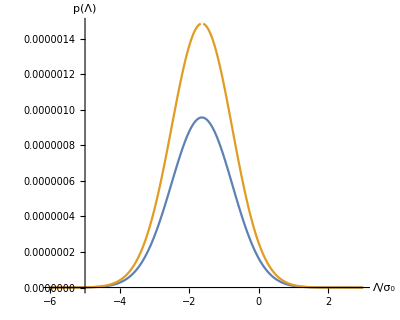

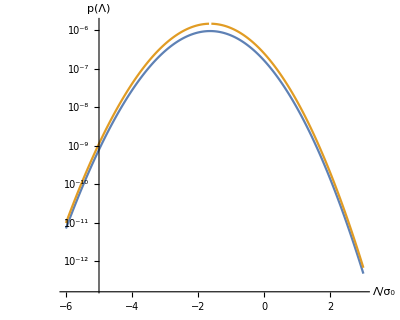

```mathematica
p3= ListPlot[{list7,list8},Joined->True,Joined->True,InterpolationOrder->3,AxesLabel->{"Λ/σ_0","p(Λ)"},BaseStyle->{FontWeight->"Normal",FontFamily->"Times",FontSize->18},AxesOrigin->{-5,0},AspectRatio->.8]
p4 = ListLogPlot[{list7,list8},Joined->True,Joined->True,InterpolationOrder->3,AxesLabel->{"Λ/σ_0","p(Λ)"},BaseStyle->{FontWeight->"Normal",FontFamily->"Times",FontSize->18},AxesOrigin->{-5,Automatic},AspectRatio->.8]
```

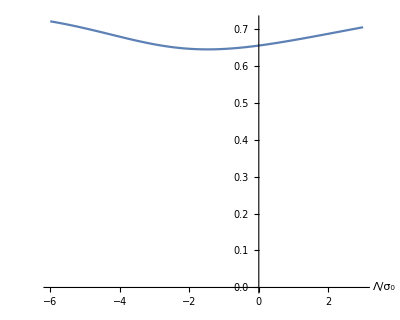

```mathematica
p5 = ListPlot[Transpose[{Transpose[list7][[1]],Transpose[list7][[2]]/Transpose[list8][[2]]}],Joined->True,PlotRange->{0,All},Joined->True,Joined->True,InterpolationOrder->3,AxesLabel->{"Λ/σ_0",""},BaseStyle->{FontWeight->"Normal",FontFamily->"Times",FontSize->18},AxesOrigin->{-0,Automatic},AspectRatio->.8]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\User\Dropbox\PhD project\Mathematica notebooks\Min and saddles\richard

```mathematica
Export["../Gaussian-RF-paper/PLam_approx.eps",p3]
Export["../Gaussian-RF-paper/PLam_approx_log.eps",p4]
Export["../Gaussian-RF-paper/PLam_ratio.eps",p5]
```

```mathematica
Export["PLam_approx.eps",p3]
Export["PLam_approx_log.eps",p4]
Export["PLam_ratio.eps",p5]
```

PLam_approx.eps

PLam_approx_log.eps

PLam_ratio.eps

```mathematica
SystemOpen["PLam_ratio.eps"]
```

```mathematica
list9 = Table[{Nval, Total[Exp[ParallelTable[findProbVapproxWork2[.2,Nval,z,0],{z,-4,0,.1}]  -findProbAllWork2[.2,Nval,0]]].1},{Nval,3,30,3}];
```

```mathematica
list10 = Table[{Nval, Total[Exp[ParallelTable[findProbVapproxWork2[.5,Nval,z,0],{z,-4,0,.1}]  -findProbAllWork2[.5,Nval,0]]].1},{Nval,3,30,3}];

list11 = Table[{Nval, Total[Exp[ParallelTable[findProbVapproxWork2[.8,Nval,z,0],{z,-4,0,.1}]  -findProbAllWork2[.8,Nval,0]]].1},{Nval,3,30,3}];

list12 = Table[{Nval, Total[Exp[ParallelTable[findProbVapproxWork2[.9,Nval,z,0],{z,-4,0,.1}]  -findProbAllWork2[.9,Nval,0]]].1},{Nval,3,30,3}];
```

```mathematica
p6=ListLogPlot[{list9,list10,list11,list12},Joined->True,PlotRange->{Automatic,11},Joined->True,InterpolationOrder->3,AxesLabel->{"N","P(Λ>0|N,γ)"},BaseStyle->{FontWeight->"Normal",FontFamily->"Times",FontSize->14}]
```

ListLogPlot::ioproc: {{3.,Log[0.1 (2.71828^(Times[«2»]+findProbVapproxWork2[«4»])+2.71828^(Times[«2»]+findProbVapproxWork2[«4»])+«37»+2.71828^(Times[«2»]+findProbVapproxWork2[«4»])+2.71828^(Times[«2»]+findProbVapproxWork2[«4»]))]},«8»,{30.,Log[0.1 ((«18»)^(«1»)+«39»+(«18»)^(«1»+«1»))]}} may contain non-machine-precision numbers, complex numbers, or invalid entries.

General::stop: Further output of ListLogPlot::ioproc will be suppressed during this calculation.

-Graphics-

```mathematica
Export["../Gaussian-RF-paper/pwithN.eps",p6]
```

../Gaussian-RF-paper/pwithN.eps

```mathematica
list9a = Table[{Nval, Total[Exp[ParallelTable[findProbVapproxWork2[.2,Nval,z,0],{z,0,0,.1}]  -findProbAllWork2[.2,Nval,0]]]},{Nval,3,30,3}];
```

```mathematica
list10a = Table[{Nval, Total[Exp[ParallelTable[findProbVapproxWork2[.5,Nval,z,0],{z,0,0,.1}]  -findProbAllWork2[.5,Nval,0]]]},{Nval,3,30,3}];

list11a = Table[{Nval, Total[Exp[ParallelTable[findProbVapproxWork2[.8,Nval,z,0],{z,0,0,.1}]  -findProbAllWork2[.8,Nval,0]]]},{Nval,3,30,3}];

list12a = Table[{Nval, Total[Exp[ParallelTable[findProbVapproxWork2[.9,Nval,z,0],{z,0,0,.1}]  -findProbAllWork2[.9,Nval,0]]]},{Nval,3,30,3}];
```

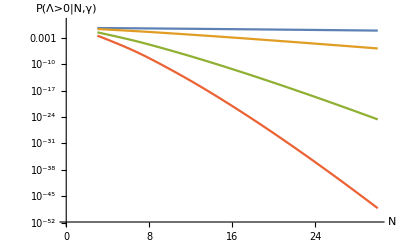

```mathematica
p6a = ListLogPlot[{list9a,list10a,list11a,list12a},Joined->True,PlotRange->{Automatic,11},Joined->True,InterpolationOrder->3,AxesLabel->{"N","P(Λ>0|N,γ)"},BaseStyle->{FontWeight->"Normal",FontFamily->"Times",FontSize->14}]
```

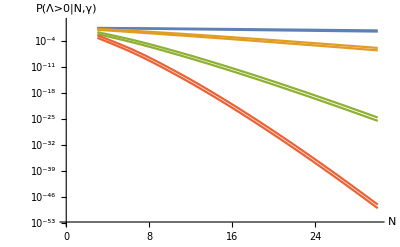

```mathematica
Show[p6,p6a]
```

```mathematica
list12
```

{{3,0.00076072},{6,2.42652×10^-7},{9,1.837×10^-11},{12,4.62345×10^-16},{15,4.82477×10^-21},{18,2.43304×10^-26},{21,6.62971×10^-32},{24,1.06236×10^-37},{27,1.06957×10^-43},{30,7.134×10^-50}}